√(-L^2/4+1/6 L^2 (2-3/(n^2 π^2)))

√(n^2/L^2) π

state→1→0.567862

entropy infotmatik→1→2.21196

General::ivar: 1 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

state→2→1.67029

entropy infotmatik→2→2.60673

state→3→2.6272

entropy infotmatik→3→2.75255

state→4→3.55802

entropy infotmatik→4→2.82819

state→5→4.47903

entropy infotmatik→5→2.87423

state→6→5.39526

entropy infotmatik→6→2.90512

state→7→6.30879

entropy infotmatik→7→2.92697

state→8→7.22066

entropy infotmatik→8→2.94331

state→9→8.13141

entropy infotmatik→9→2.95554

state→10→9.04139

entropy infotmatik→10→2.96528

state→11→9.9508

entropy infotmatik→11→2.97255

state→12→10.8598

entropy infotmatik→12→2.97865

state→13→11.7685

entropy infotmatik→13→2.98286

state→14→12.6769

entropy infotmatik→14→2.98664

state→15→13.5851

entropy infotmatik→15→2.98859

state→16→14.4932

entropy infotmatik→16→2.99066

state→17→15.4011

entropy infotmatik→17→2.99065

state→18→16.3089

entropy infotmatik→18→2.99127

state→19→17.2166

entropy infotmatik→19→2.98919

state→20→18.1242

entropy infotmatik→20→2.98835

General::ivar: 20. is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

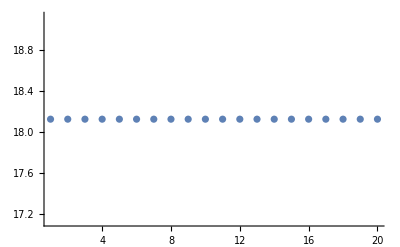

General::ivar: 20. is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

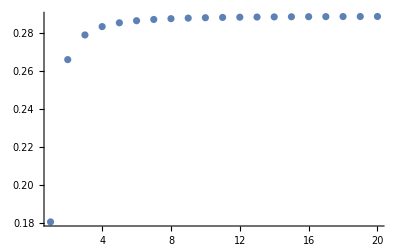

General::ivar: 20. is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

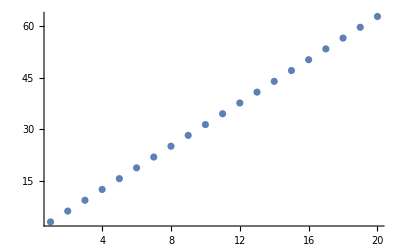

-Graphics-

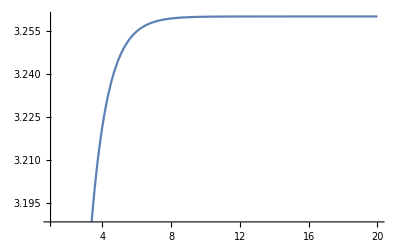

-Graphics-

```mathematica
Clear["Global`*"]
$TextStyle={FontSize->12};
(* Προσπάθησα και με την "έτοιμη" εντολή αλλά έκανα κάτι λάθος και δεν μπόρεσα να την τρέξω οι εντολές ήταν :
<<Calculus'FourierTransform' & FourierTrigSeries*)
L=1;

u[n_,x_]:=√(2/L) Sin [n*Pi*x/L];
p[k_,n_]=1/Sqrt[2*Pi]*Integrate[u[n,x]*Exp[-I*k*x],{x,0,L}];
Clear[L]
(*possition*)
mx=Simplify[Integrate[u[n,x]^2*x,{x,0,L}],Element[n,Integers]];
mx2=Simplify[Integrate[u[n,x]^2*x^2,{x,0,L}],Element[n,Integers]];
Δχ[n_]=Sqrt[mx2-mx^2]
(*momentum*)
k@u_=-I*D[u[x,n],x];
k2@u_=-D[u[x,n],{x,2}];
mk=Simplify[Integrate[u[x,n]*k@u,{x,0,L}],Element[n,Integers]];
mk2=Simplify[Integrate[u[x,n]*k2@u,{x,0,L}],Element[n,Integers]];
Δk[n_]=Sqrt[mk2-mk^2]
(*first of 20*)
L=1;
j=L*k;
ksi[n_,k_]=((1-Cos[1*k]*(-1)^n)2 *Pi*1*n^2)/(((n *Pi-1*k)^2)*((n*Pi+1*k)^2));
Sx [n_]=Log[2.0]-1;
Sx=Log[2*L]-1;
Sk[n_]:=-NIntegrate[ksi[n,k]*Log[ksi[n,k]],{k,-100,100},AccuracyGoal->10];

For[n=1,n<21,n+=1,

av=N[Δχ[n]*Δk[n]]; 

S[n_]=Sx+Sk[n];
Print[  state -> n->av ];
Print[infotmatik entropy -> n -> N[S[n]]];

avevaiotita[n_]=Δχ[n*1.0]*Δk[n*1.0];
rG=Array[avevaiotita,n];
rdx=Array[Δχ,n];
rdk=Array[Δk,n];
fG[n_]=Fit[rG,{1,n,n^2},n];
fdx[n_]=Fit[rdx,{1,n,n^2},n];
fdk[n_]=Fit[rdk,{1,n,n^2},n];

];
 Show[ListPlot[rG],Plot[fG[n],{n,0,20}],PlotRange->All]
Show[ListPlot[rdx],Plot[fdx[n],{n,0,20}],PlotRange->All]
Show[ListPlot[rdk],Plot[fdk[n],{n,0,20}],PlotRange->All]      
fk=Table[Sk[x],{x,20}];
fx=Table[Sx[x],{x,20}];
f=Table[Sk[x]+Sx[x],{x,20}];
Fkfit[x_]=Fit[fk,{1,E^-x},x];
Fxfit[x_]=Fit[fx,{1,E^-x},x];
Ffit[x_]=Fit[f,{1,E^-x},x];
Plot[Fxfit[x],{x,1,20}]
Plot[Fkfit[x],{x,1,20}]
Plot[Ffit[x],{x,1,20}]
```